```mathematica
(*F = ma sprendinys*)
Clear[F,m,c]
(*Solve the differential equation*)
sol1=DSolve[{z''[t]==F/m*Sqrt[1-(z'[t]/c)^2],z[0]==0,z'[0]==0},z[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{z[t]→(-c^2 m+c^2 m Cos[(F t)/(c m)])/F},{z[t]→(c^2 m+c^2 m Cos[(-c m π+F t)/(c m)])/F}}

```mathematica
(*Define the parameters*)
(*F=10; (*Force*)*)
m=0.005; (*Mass*)
c=3*10^8; (*Speed of light*)
```

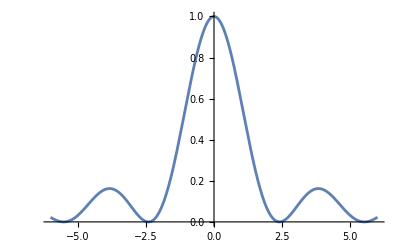

```mathematica
Plot[Abs[BesselJ[0,x]]^2,{x,-6,6}]
```

```mathematica
(*Duoda atstumą iki pirmo nulio*)
N[BesselJZero[0,1]]
```

2.40483

```mathematica
(* Burės paviršiaus plotas () *)
Sail=2*Pi*Integrate[x,{x,0,N[BesselJZero[0,1]]}]
```

18.1684

```mathematica
(*Intensyvumo funkcija paveikta x operatoriumi ir suintegruota.
Gaunasi vidutinė intensyvumo reikšmė per visą paviršių*)
Beselis=2*Pi*Integrate[x*Abs[BesselJ[0,x]]^2,{x,0,N[BesselJZero[0,1]]}]
```

4.89664

```mathematica
Clear[F]
P = 1000000; (*Beam overall power*)
(*Force acting on sail*)
F = 4*Pi*P/c*Integrate[x*Abs[BesselJ[0,x]]^2, {x, 0, N[BesselJZero[0,1]]}]
```

0.0326443

```mathematica
(*Extract the solution function*)
zSol[t_]=z[t]/. sol1[[2]];
(*Plot the solution*)
Manipulate[Plot[zSol[t],{t,0,tMax},PlotRange->{{0,tMax},Automatic},AxesLabel->{"t","z(t)"},PlotLabel->"Solution to the Differential Equation",GridLines->Automatic],
{{tMax,10,"Maximum Time"},1,1000,1}
]
```